Your Title Here

```mathematica
r=1;a=4*r;
```

```mathematica
(*equations for bottom and top of first (left) flask*)
```

```mathematica
f1b[x_]=-√(r^2-x^2)+r;
```

```mathematica
f1t[x_]=√(r^2-x^2)+r;
```

```mathematica
(*equations for bottom and top of second (right) flask*)
```

```mathematica
f2b[x_]=-√(r^2-x^2-a^2+2*x*a)+r;
```

```mathematica
f2t[x_]=√(r^2-x^2-a^2+2*x*a)+r;
```

```mathematica
(*equations for curves connecting flasks*)
```

```mathematica
tube1[x_]:=-0.1977*x^2+0.791*x+2.209;
```

```mathematica
tube2[x_]:=-0.2409*x^2+0.9634*x+1.687;
```

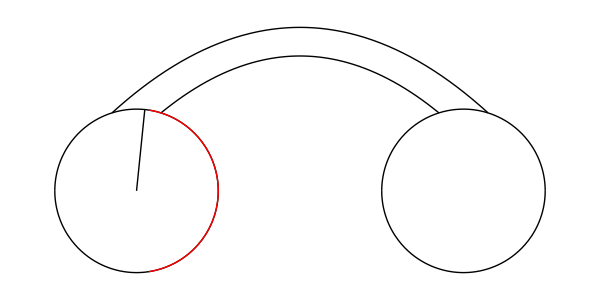

```mathematica
flasks=Show[
Plot[{f1b[x],f1t[x]},{x,-r,r},PlotStyle->{{Thick,Black}}],
Plot[{f2b[x],f2t[x]},{x,a-r,a+r},PlotStyle->{{Thick,Black}}],
Plot[tube1[x],{x,-0.3*r,a+0.3*r},PlotStyle->{Thick,Black}],
Plot[tube2[x],{x,0.3*r,a-0.3*r},PlotStyle->{Thick,Black}],
PlotRange->{{-r,a+r},{0,3*r}},Axes->False,ImageSize->{600,400},AspectRatio->0.5,
Epilog->{
(*{PointSize@0.02,Point@{-0.3*r,f1t[-0.3*r]},Point@{a+0.3*r,f2t[a+0.3*r]},Blue,Point@{0.3*r,f1t[0.3*r]},Point@{a-0.3*r,f2t[a-0.3*r]}},*)
{Thick,Red,Circle[{0,r},r,{ArcTan[f1t[0.3*r]/(0.3*r)],ArcTan[f1t[-0.3*r]/(-0.3*r)]}]},
Line[{{0,r},{r*Cos[ArcTan[(r+f1t[0.3*r])/(0.3*r)]],r+r*Sin[ArcTan[(r+f1t[0.3*r])/(0.3*r)]]}}],
(*{Thickness@0.01,GrayLevel@0.3,Circle[{0,r},r,{π/4,3*π/4}],Circle[{a,r},r,{π/4,3*π/4}]},*)
(*{Thickness@0.01,GrayLevel@0.3,Circle[{0,r},r,{π/4*(1+go[1]),π/4*(3-go[1])}],Circle[{a,r},r,{π/4*(1+go[1]),π/4*(3-go[1])}]},*)
}]
```

```mathematica
tubes=Show[
Plot[tube1[x],{x,-0.3*r,a+0.3*r},PlotStyle->{Thick,Black}],
Plot[tube2[x],{x,0.3*r,a-0.3*r},PlotStyle->{Thick,Black}],
PlotRange->{{-r,a+r},{0,3*r}},Axes->False,ImageSize->{600,400},AspectRatio->0.5];
```





```mathematica
Manipulate[
Module[{fill1,fill2},
fill1=Rescale[h1,{-0.01,2*r}];fill2=Rescale[h2,{-0.01,2*r}];

Show[tubes,Epilog->{
{Cyan,
DiskSegment[{0,r},r,{(270°-180°*fill1),(270°+180°*fill1)}],
DiskSegment[{a,r},r,{(270°-180°*fill2),(270°+180°*fill2)}]},
{Thick,Circle[{#,r},r]&/@{0,a}}
}]
],
Grid@{{
"height of fluid",
Control[{{h1,r,"left flask"},0,2*r,0.1,Appearance->"Labeled",ImageSize->Small}],
Control[{{h2,0.5*r,"right flask"},0,2*r,0.1,Appearance->"Labeled",ImageSize->Small}]
}},
SaveDefinitions->True]
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX